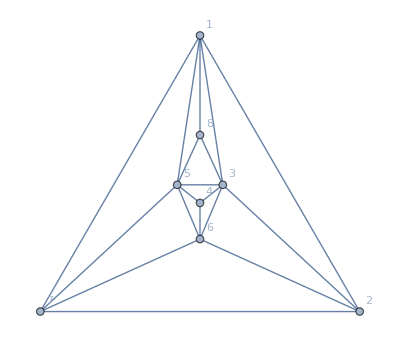

```mathematica
Graph[ReadGrof[20],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
HandleGraph[g_,op_:Last]:=Block[{result={},current=g,edge},
AppendTo[result,Labeled[current,{edge,EdgeCount[current]},{Top,Bottom}]]
While[!CompleteGraphQ[current],
edge=op[EdgeList[GraphComplement[current]]];
current=VertexContract[current,{edge[[1]],edge[[2]]}];
PrintTemporary[current];
AppendTo[result,Labeled[current,{edge,EdgeCount[current]},{Top,Bottom}]]
];
result
]
```

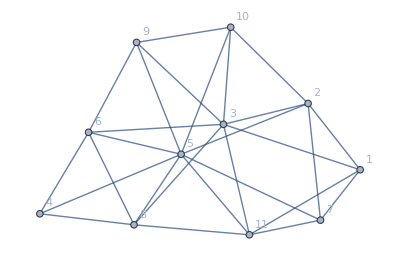
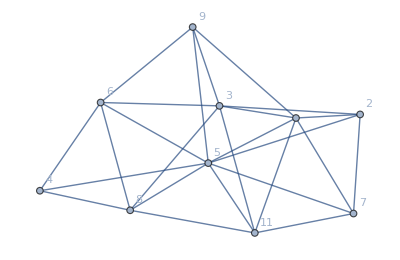
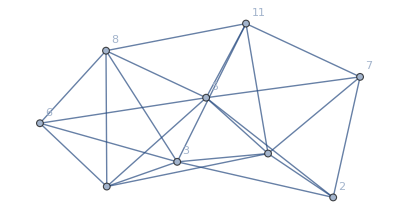
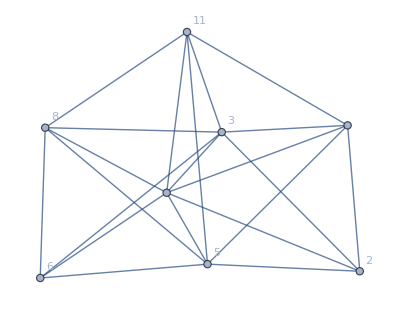
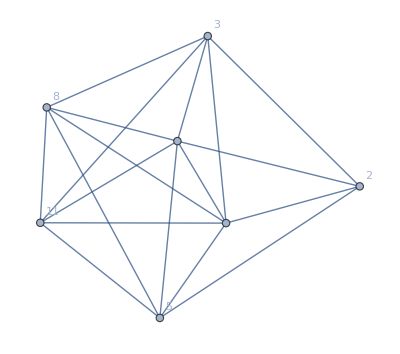
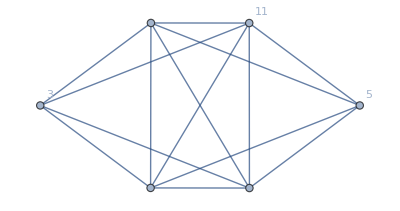
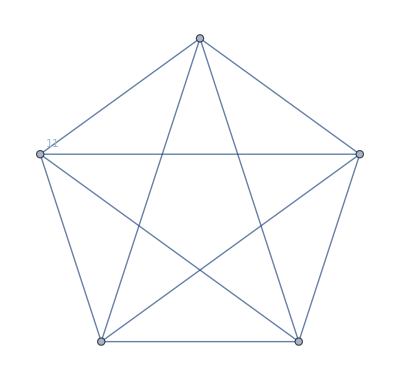
{-Graphics-1<->1027,-Graphics-1<->1025,-Graphics-9<->423,-Graphics-7<->921,-Graphics-6<->118,-Graphics-2<->814,-Graphics-3<->510}

```mathematica
HandleGraph[Graph[ReadGrof[500],VertexLabels->"Name"],RandomChoice]
```

```mathematica
FindFullFormula4[Graph[ReadGrof[500],VertexLabels->"Name"]]
```

{v149x26bx35x78a,v189x24bx35x67a,v18x249bx35x67a,v189x26bx35x47a,v16x249bx35x78a,v18ax26bx35x479,v14ax26bx35x789,v16ax24bx35x789,v16ax249bx35x78,v18ax249bx35x67,v15x289x347x6ab}